```mathematica
Needs["AMOP`"];
Needs["Thesis`"];
```

```mathematica
data=Get[$nb <> "out/fig4c.wl"];

pts[k_]:=Transpose[{data[k<>"__ell_over_xi_sq"],MapThread[Around,{data[k<>"__rate"],data[k<>"__rate_err"]}]}];
```

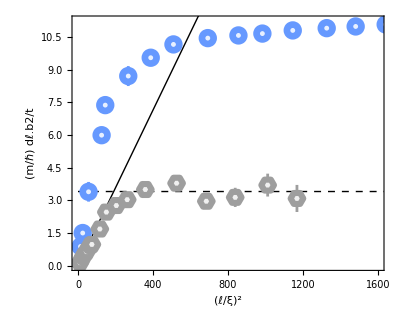

```mathematica
Show[
ListPlot[{pts["wke_all"],pts["exp"]},
PlotStyle->{StandardBlue,cc},
Prolog->{Line[{{0,0},{2100,2100/56}}],Dashed,Line[{{0,3.4},{2100,3.4}}]},
PlotMarkers->{MarkerCirc[12,cc], MarkerHexa[12,StandardGray]},
PlotRange->{{0,1600},{0,All}}, AspectRatio->0.8,FrameLabel->{"(ℓ/ξ\!\(\*SuperscriptBox[\()\), \(2\)]\)","(m/ℏ) dℓ.b2/dt"}]
]
```